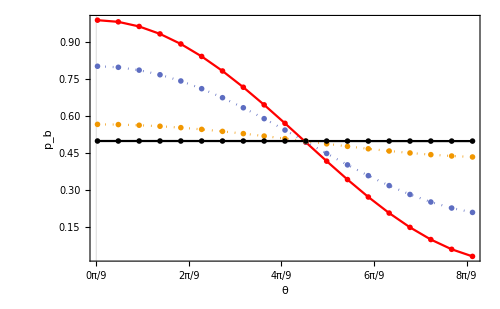

```mathematica
ClearAll;

(*Define the function p*)
p[s_,θ_]:=Cos[θ/2]^2*1/2*((1+Exp[-2 s^2])+Tan[θ/2]^2*(1-Exp[-2 s^2]));

(*Define the list of s values*)
sList={0.1,0.5,1,2};

(*Data for all s values*)
dataShort=Table[Table[{θ,p[s,θ]},{θ,0.01,10 Pi/11,Pi/20}],{s,sList}];

(*Ticks for the θ axis*)
thetaTicks=Table[{2 n Pi/9,Row[{2 n,"π/9"}]},{n,0,6}];

(*Plot all the data with different styles for s=2*)
plotMain=ListPlot[dataShort,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->Table[If[s==2,Black,If[s==0.1,Red,Dotted]],{s,sList}],PlotTheme->"Scientific",PlotLegends->Placed[StringForm["s=``",#]&/@sList,{Left,Bottom}]];

(*Show the plot*)
Show[plotMain,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks,None}},PlotRange->All,AspectRatio->0.618,ImageSize->500,FrameLabel->{"θ","p_b"},LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0],Bold}]
(*Show the plot*)plotFinal=Show[plotMain,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks,None}},PlotRange->All,AspectRatio->0.618,ImageSize->500,FrameLabel->{"θ","\!\(\*SubscriptBox[\(p\), \(b\)]\)"},LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0],Bold}];

(*保存为 PNG*)
Export["C:\\Users\\YaoXiaoxi\\Desktop\\8.30byYao Xiaoxi\\Figs\\Fig2.png",plotFinal,ImageResolution->300];
```

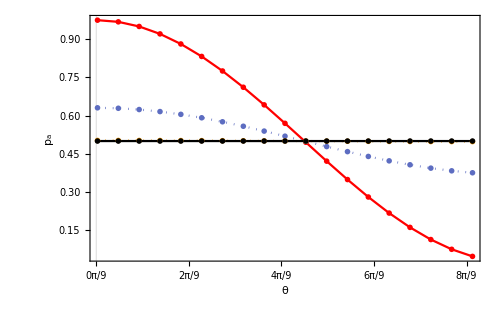

```mathematica
ClearAll;

(*Define the function p*)
p[s_,θ_]:=Cos[θ/2]^2*1/2*((1+Exp[-2 s^2])+Tan[θ/2]^2*(1-Exp[-2 s^2]));

(*Define the list of original and scaled s values*)
sOriginal={0.1,0.5,1,2};
sList=1.64*sOriginal;   (*计算时用放大的*)

(*Data for all s values*)
dataShort=Table[Table[{θ,p[s,θ]},{θ,0.01,10 Pi/11,Pi/20}],{s,sList}];

(*Ticks for the θ axis*)
thetaTicks=Table[{2 n Pi/9,Row[{2 n,"π/9"}]},{n,0,6}];

(*Plot all the data with hollow markers*)
plotMain=ListPlot[dataShort,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->Table[If[s==1.64*2,Black,If[s==1.64*0.1,Red,Dotted]],{s,sList}],PlotTheme->"Scientific",PlotLegends->Placed[StringForm["s=``",#]&/@sOriginal,{Left,Bottom}]  (*✅ 用原始数值做图例*)];

(*Show the plot*)
Show[plotMain,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks,None}},PlotRange->All,AspectRatio->0.618,ImageSize->500,FrameLabel->{"θ","\!\(\*SubscriptBox[\(p\), \(a\)]\)"},LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0],Bold}]
(*Show the plot*)plotFinal=Show[plotMain,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks,None}},PlotRange->All,AspectRatio->0.618,ImageSize->500,FrameLabel->{"θ","\!\(\*SubscriptBox[\(p\), \(a\)]\)"},LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0],Bold}];

(*保存为 PNG*)
Export["C:\\Users\\YaoXiaoxi\\Desktop\\8.30byYao Xiaoxi\\Figs\\Fig3.png",plotFinal,ImageResolution->300];
```

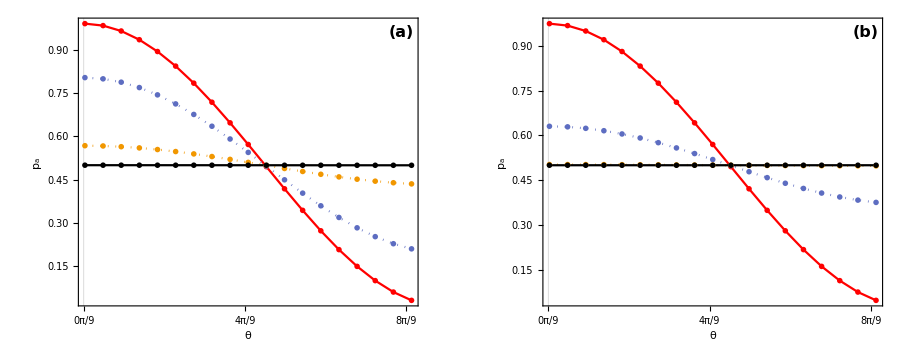

```mathematica
(*生成第一幅图*)p1[s_,θ_]:=Cos[θ/2]^2*1/2*((1+Exp[-2 s^2])+Tan[θ/2]^2*(1-Exp[-2 s^2]));
sList1={0.1,0.5,1,2};
dataShort1=Table[Table[{θ,p1[s,θ]},{θ,0.01,10 Pi/11,Pi/20}],{s,sList1}];
thetaTicks1=Table[{2 n Pi/9,Row[{2 n,"π/9"}]},{n,0,6}];
plotMain1=ListPlot[dataShort1,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->Table[If[s==2,Black,If[s==0.1,Red,Dotted]],{s,sList1}],PlotTheme->"Scientific",PlotLegends->Placed[StringForm["s=``",#]&/@sList1,{Left,Bottom}]];
plotFinal1=Show[plotMain1,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks1,None}},PlotRange->All,AspectRatio->0.818,ImageSize->400,(*Modified to 1 for square*)FrameLabel->{"θ","\!\(\*SubscriptBox[\(p\), \(a\)]\)"},LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0],Bold}];

(*生成第二幅图*)
p2[s_,θ_]:=Cos[θ/2]^2*1/2*((1+Exp[-2 s^2])+Tan[θ/2]^2*(1-Exp[-2 s^2]));
sOriginal={0.1,0.5,1,2};
sList2=1.64*sOriginal;
dataShort2=Table[Table[{θ,p2[s,θ]},{θ,0.01,10 Pi/11,Pi/20}],{s,sList2}];
thetaTicks2=Table[{2 n Pi/9,Row[{2 n,"π/9"}]},{n,0,6}];
plotMain2=ListPlot[dataShort2,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->Table[If[s==1.64*2,Black,If[s==1.64*0.1,Red,Dotted]],{s,sList2}],PlotTheme->"Scientific",PlotLegends->Placed[StringForm["s=``",#]&/@sOriginal,{Left,Bottom}]];
plotFinal2=Show[plotMain2,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks2,None}},PlotRange->All,AspectRatio->0.818,ImageSize->400,(*Modified to 1 for square*)FrameLabel->{"θ","\!\(\*SubscriptBox[\(p\), \(a\)]\)"},LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0],Bold}];

(*添加标签并组合图形-修改为图内右上角*)
labeledPlot1=Legended[plotFinal1,Placed[Style["(a)",16,Bold,FontFamily->"Times New Roman"],Scaled[{0.95,0.95}]]];
labeledPlot2=Legended[plotFinal2,Placed[Style["(b)",16,Bold,FontFamily->"Times New Roman"],Scaled[{0.95,0.95}]]];
combinedPlot=GraphicsRow[{labeledPlot1,labeledPlot2},ImageSize->900];

(*显示并导出图形*)
Print[combinedPlot];
Export["C:\\Users\\YaoXiaoxi\\Desktop\\8.30byYao Xiaoxi\\Figs\\Fig3.png",combinedPlot,ImageResolution->300];
```

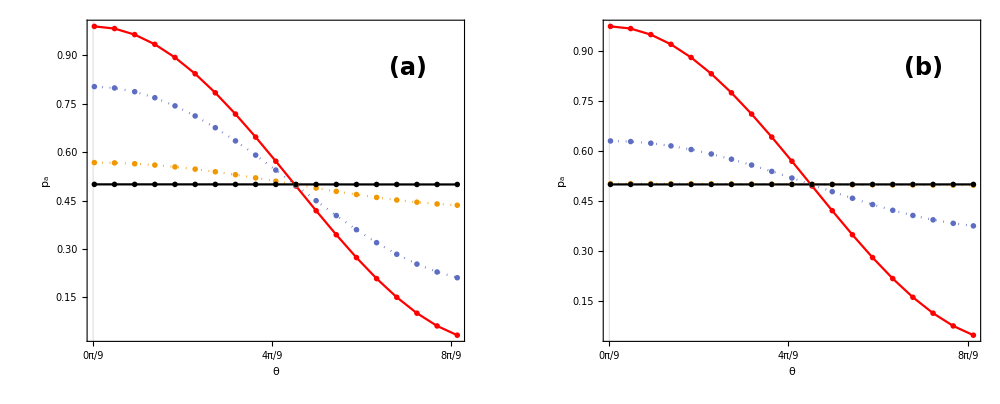

```mathematica
(*定义函数*)p1[s_,θ_]:=Cos[θ/2]^2*1/2*((1+Exp[-2 s^2])+Tan[θ/2]^2*(1-Exp[-2 s^2]))
p2[s_,θ_]:=Cos[θ/2]^2*1/2*((1+Exp[-2 s^2])+Tan[θ/2]^2*(1-Exp[-2 s^2]))

(*参数列表*)
sList1={0.1,0.5,1,2};
sOriginal={0.1,0.5,1,2};
sList2=1.64*sOriginal;
thetaTicks=Table[{2 n Pi/9,Style[Row[{2 n,"π/9"}],24]},{n,0,6}];

(*数据*)
dataShort1=Table[Table[{θ,p1[s,θ]},{θ,0.01,10 Pi/11,Pi/20}],{s,sList1}];
dataShort2=Table[Table[{θ,p2[s,θ]},{θ,0.01,10 Pi/11,Pi/20}],{s,sList2}];

(*图1*)
plotMain1=ListPlot[dataShort1,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->Table[If[s==2,Black,If[s==0.1,Red,Dotted]],{s,sList1}],PlotTheme->"Scientific",PlotLegends->Placed[Style[#,24,Bold]&/@(StringForm["s=``",#]&/@sList1),{Left,Bottom}]];

plotFinal1=Show[plotMain1,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks,None}},PlotRange->All,AspectRatio->0.818,ImageSize->450,FrameLabel->{Style["θ",24,Bold],Style[Subscript["p","a"],24,Bold]},LabelStyle->Directive[FontFamily->"Times New Roman",GrayLevel[0],24]];

(*图2*)
plotMain2=ListPlot[dataShort2,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->Table[If[s==1.64*2,Black,If[s==1.64*0.1,Red,Dotted]],{s,sList2}],PlotTheme->"Scientific",PlotLegends->Placed[Style[#,24,Bold]&/@(StringForm["s=``",#]&/@sOriginal),{Left,Bottom}]];

plotFinal2=Show[plotMain2,Frame->True,FrameTicks->{{Automatic,None},{thetaTicks,None}},PlotRange->All,AspectRatio->0.818,ImageSize->450,FrameLabel->{Style["θ",24,Bold],Style[Subscript["p","a"],24,Bold]},LabelStyle->Directive[FontFamily->"Times New Roman",GrayLevel[0],24]];

(*添加图内标签*)
labeledPlot1=Show[plotFinal1,Epilog->{Inset[Style["(a)",24,Bold,FontFamily->"Times New Roman"],Scaled[{0.85,0.85}]]}];
labeledPlot2=Show[plotFinal2,Epilog->{Inset[Style["(b)",24,Bold,FontFamily->"Times New Roman"],Scaled[{0.85,0.85}]]}];

(*组合图*)
combinedPlot=GraphicsRow[{labeledPlot1,labeledPlot2},ImageSize->1000];

(*显示并导出*)
Print[combinedPlot];
Export["C:\\Users\\YaoXiaoxi\\Desktop\\Paper909\\Figs\\Fig3.png",combinedPlot,ImageResolution->300];
```